Systems Cell Biology
Autoregulation in Transcription and Rate-Balance Plots 
Copyright by Proferssor Lee Bardwell, University of California, Irvine

Graphical Analysis of Steady-State
Simple Gene Regulation

```mathematica
ClearAll["Global`*"]
```

```mathematica
Manipulate[ (* Rate balance plot for simple gene regulation *)
Plot[{P ,r*Y} , {Y, 0,12}, 
PlotRange-> {0,10},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Simple Gene Regulation"],
{{P, 3}, 0, 10,Appearance->"Labeled"},
{{r, 0.5}, 0.01, 2,Appearance->"Labeled"}]
```

Graphical Analysis of Steady-State
Negative Autoregulation

```mathematica
Manipulate[ (* Rate balance plot for negatively-autoregulated gene *)
Plot[{P k^n/(k^n+Y^n) ,r*Y} , {Y, 0, Ymax}, 
PlotRange-> {0,P*1.1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Negative Autoregulation"],
{{P, 1}, 0, 10,Appearance->"Labeled"},
{{k, 1}, 0, 10,Appearance->"Labeled"}, 
{{n, 1}, 0.1, 10,Appearance->"Labeled"},
{{r, 0.1}, 0.01, 2,Appearance->"Labeled"},
{{Ymax, 10}, 1, 100,Appearance->"Labeled"}]
```

Positive Autoregulation - a transcription factor that is the only activator of its own gene

Background:
If a transcription factor TF regulates the expression of a gene Y, we can describe this as

Y'[t]=P (TF[t]^n/(k^n+TF[t]^n)) - r Y[t]	(Scheme 1)

Where the blue part is called the input function and the red part we  call the decay function.
The parameter n is called the Hill coefficient.

Analysis 1:
Statement 1: At steady-state, we obtain Yss = P/dTF[t]^n/(k^n+TF[t]^n).
Statement 2: The maximum value that the expression TF[t]^n/(k^n+TF[t]^n) can assume is 1.
Statement 3: Given statements 1 and 2, the maximum steady state value of Y (i.e. the max value of Yss) is P/d.
Statement 4: For n =1, in order for TF[t]^n/(k^n+TF[t]^n) to approach its maximum value of 1, TF[t]needs to be much greater than k.
Statement 5: For n large, in order for TF[t]^n/(k^n+TF[t]^n) to approach its maximum value of 1, TF[t]needs to be greater than k.


To construct the scenario "a transcription factor that is the only activator of its own gene" we substitute Y for TF, above, to get

   Y'[t]=P (Y[t]^n/(k^n+Y[t]^n)) - r Y[t]	          (Scheme 2)
	     forward rate - reverse rate
Analysis 2:

Statement 6: Now, Yss = 0 is a steady-state solution, but it's not the only steady-state solution.  It's not so easy to calculate the other steady-state value(s) of TF.  We will do it for some values of n further below.

Statement 7: Nevertheless, Statement 2 still applies to Scheme 2.  Given that, it is still true that the maximum conceivably possible steady state value of Y is P/d

Statement 8: Statement 4 also still applies to Scheme 2.  Considering Statements 4 and 7 together implies that P/d needs to be much greater than k in order for TFss to approach its max of P/d.

Graphical Analysis of Steady-State
Positive Autoregulation

   Y=P (Y^n/(k^n+Y^n)) - r Y	        
          forward rate - reverse rate

```mathematica
ClearAll["Global`*"]

Manipulate[ (* Rate balance plot for positively-autoregulated gene *)
Plot[{P Y^n/(k^n+Y^n),Y*r} , {Y, 0, Ymax}, 
PlotRange-> {0,Xmax},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation"],
{{P, 1}, 0, 10,Appearance->"Labeled"},
{{k, 3}, 0, 10,0.1,Appearance->"Labeled"}, 
{{n, 1}, 0, 10,1,Appearance->"Labeled"},
{{r, 0.1}, 0.01, 2,Appearance->"Labeled"},
{Xmax, 1, 100,Appearance->"Labeled"},
{{Ymax, 10}, 1, 100,Appearance->"Labeled"}]
```

```mathematica
Manipulate[ (* Rate balance plot for positively-autoregulated gene *)
(* Green line is net rate.  Steady state occurs when net rate = 0 *)
Plot[{P Y^n/(k^n+Y^n),Y*r,P Y^n/(k^n+Y^n)-Y*r} , {Y, 0, Ymax}, 
PlotRange-> {-1,P*1.1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation"],
{{P, 1}, 0, 10,Appearance->"Labeled"},
{{k, 3}, 0, 10,Appearance->"Labeled"}, 
{{n, 4}, 0.1, 10,Appearance->"Labeled"},
{{r, 0.11}, 0.01, 2,Appearance->"Labeled"},
{{Ymax, 11}, 1, 100,Appearance->"Labeled"}]
```

Positive Autoregulation: A  demonstration that the zero steady state is unstable for  n=1

Below we will use a technique involving Table and ListPlot to get an input-output function.  
The input will be the starting concentration of Y (i.e. the initial condition, Y[0]). 
The output will be the steady-state concentration of Y.  
This technique involves calling NDSolve 501 times, each time varying the value of Y[0] (from 0 to 5 in increments of 0.01).

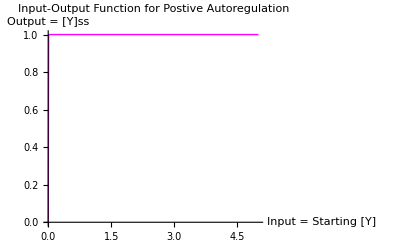

```mathematica
system1 ={ 
Y'[t]==P(Y[t]^n/(k^n+Y[t]^n))-r Y[t]
};
initials1 = {Y[0]== i};
parameters1 = {P->2, k->1 , n->1, r->1};
fullsystem2= Join[system1, initials1];

myTable =
Table[
{i, 
Y[t]/.Flatten[NDSolve[fullsystem2/.parameters1, 
{Y[t]}, {t, 0, 400}]] /.t -> 400 }, (* 400 seconds is sufficient time to "reach" steady state *)
{i, 0,5, 0.01}];

ListPlot[myTable, 
Joined ->True, PlotRange -> All, PlotStyle -> {Magenta, Thick},
AxesLabel->{"Input = Starting [Y]","Output = [Y]ss"}, PlotLabel-> "Input-Output Function for Postive Autoregulation"]
```

To do: Change n to 2 in "parameters2" and see what happens to the input-output function.  Does this tells you something about the stability of the zero steady-state?

Positive Autoregulation: A simple demonstration that the zero steady state is unstable for  n=1
Here we see that even if you start with a very very small starting concentration of Y (i.e. the initial condition, Y[0]), the system will evolve to the steady state Yss = P/r- k.

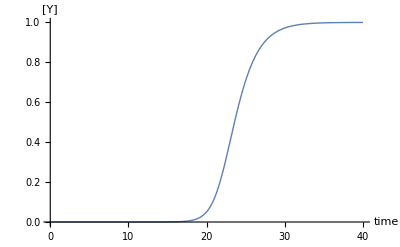

```mathematica
initials2 = {Y[0]== 0.0000000001};
fullsystem2= Join[system1, initials2];
parameters2 = {P->2, k->1 , n->1, r->1};
solset1=NDSolve[fullsystem2/.parameters2,{Y[t]}, {t,0,40}];
Plot[{Y[t]}/.solset1, {t, 0, 40}, PlotRange-> {0, Automatic}, PlotStyle->Thick, AxesLabel->{"time", "[Y]"}]
```

Optional exercise: Convince yourself that the steady-state in system1, above is P/r- k

Positive Autoregulation: Solution and analysis of the steady state for n = 1

Analysis 3:  Below, we solve the steady state for this system when n=1.  
We see that there are two solutions, one of which is zero.  The other solution is P/r - k, which obviously has a max of P/r and will only approach this max if P/r >> k.  
If P/r <=  k then the only valid (non-negative) steady state solution is TF = 0.  In this case the decay function line touches the input function curve only at zero. 
Also, since we know that Yss = P/r - k, then we can calculate that the percent saturation of the promoter by Y is (P-r k)/P.  This will only approach 100% saturation when d or k are very small.

Summary: For the n=1 system, the requirements that a non-zero steady state exist are P/r >  k.
One can show that if also  P/r >  k, then a very small amount of Y[0] will kick off the feedback loop.  That is, if P/r >  k, then the input function curve will be above the decay line near [Y] =0. Thus, if a non-zero steady state exists, the zero steady state is unstable.  So there's no way to design this system with n = 1 so that it is resistant to noise.
(Note: for some reason, Solve outputs an error message but then outputs the correct solution)

```mathematica
ClearAll["Global`*"]
Clear[ Y,P, k, n, r]
steadyStateSystem ={ 
0==P (Y^n/(k^n+Y^n))-r Y
};
Solve[steadyStateSystem/.n->1 ,Y];
Simplify[%]
```

{{Y→0},{Y→-k+P/r}}

Positive Autoregulation: Solution and analysis of the steady state for n = 2

Analysis 4:  Below, we solve the steady state for this system when n=2.  The answer is still relatively easy to interpret.  Refer to the "Graphical Analysis of Steady-State" manipulate tool above with n = 2.
There are three steady states.  The first steady-state is Y = zero.
In order for the second and third steady states to be non-imaginary, we require we require P^2-4 r^2 k^2 >=0; that is,  P/r >= 2k.  The case were  P/r < 2k corresponds to when the decay function line touches the input function curve only at zero
In the case where  P/r = 2k, the second and third steady states have the same value, that is, they collapse into a single steady state.  This is the case where the decay function line touches the input function curve at a zero and only one other point.
If  P/r > 2k, then both the second and third steady states have biochemical meaning.  In this case the second steady state is unstable and the third, higher-valued steady state is stable.

```mathematica
Solve[steadyStateSystem/.n->2 ,Y];
Simplify[%]
```

{{Y→0},{Y→(P-√(P^2-4 k^2 r^2))/(2 r)},{Y→(P+√(P^2-4 k^2 r^2))/(2 r)}}

Exploring Parameter Space - Autoregulation

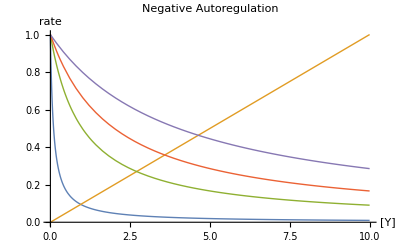

```mathematica
(* Exploring parameters in negative autoregulation *)
Plot[{
P k^n/(k^n+Y^n)/.{P-> 1, n-> 1, k-> 0.1} ,0.1*Y,
P k^n/(k^n+Y^n)/.{P-> 1, n-> 1, k-> 1} ,
P k^n/(k^n+Y^n)/.{P-> 1, n-> 1, k->2},
P k^n/(k^n+Y^n)/.{P-> 1, n-> 1, k->4}
}, {Y, 0, 10}, PlotRange-> {0,1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Negative Autoregulation"]
```

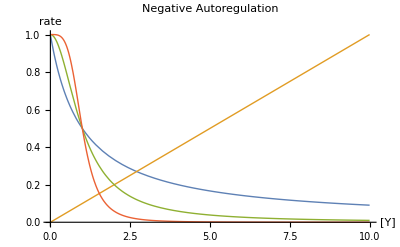

```mathematica
(* Exploring parameters in negative autoregulation *)
Plot[{
P{k^n/(k^n+Y^n)}/.{P-> 1, n-> 1, k-> 1} ,0.1*Y,
P{k^n/(k^n+Y^n)}/.{P-> 1, n-> 2, k-> 1} ,
P{k^n/(k^n+Y^n)}/.{P-> 1, n-> 4, k->1}
}, {Y, 0, 10}, PlotRange-> {0,1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Negative Autoregulation"]
```

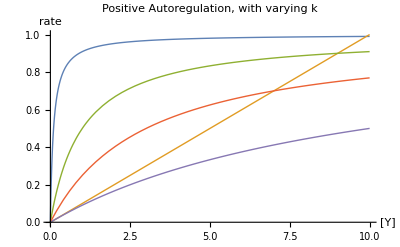

```mathematica
(* Exploring parameters in positive autoregulation *)
(* {P-> 1, r-> 0.1, n-> 1, k-> varies} *)
Plot[{
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 1, k-> 0.1} ,0.1*Y,
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 1, k-> 1} ,
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 1, k->3},

P Y^n/(k^n+Y^n)/.{P-> 1, n-> 1, k->10}
}, {Y, 0, 10}, PlotRange-> {0,1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation, with varying k"]
```

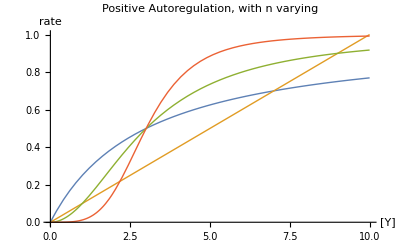

```mathematica
(* Exploring parameters in positive autoregulation *)
(* {P-> 1, r-> 0.1, n-> varies, k-> 3} *)
Plot[{
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 1, k-> 3} ,0.1*Y,
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 2, k-> 3} ,
P Y^n/(k^n+Y^n)/.{P-> 1, n-> 4, k->3}
}, {Y, 0, 10}, PlotRange-> {0,1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation, with n varying"]
```

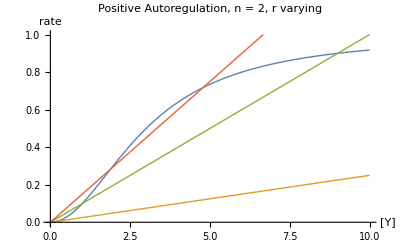

```mathematica
(* Exploring parameters in positive autoregulation *)
(* {P-> 1, r-> varies, n-> 2, k-> 3} *)
Plot[{P Y^n/(k^n+Y^n)/.{P-> 1, n-> 2, k-> 3} ,0.025*Y,0.1*Y,0.15*Y
}, {Y, 0, 10}, PlotRange-> {0,1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation, n = 2, r varying"]
```

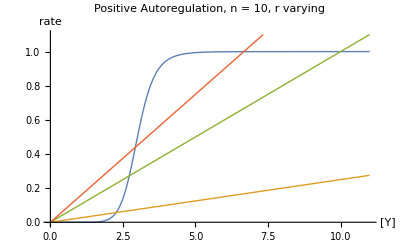

```mathematica
(* Exploring parameters in positive autoregulation *)
(* {P-> 1, r-> varies, n-> 10, k-> 3} *)
Plot[{P Y^n/(k^n+Y^n)/.{P-> 1, n-> 10, k-> 3} ,0.025*Y,0.1*Y,0.15*Y
}, {Y, 0, 11}, PlotRange-> {0,1.1},PlotStyle->Thick, AxesLabel->{"[Y]", "rate"},
PlotLabel-> "Positive Autoregulation, n = 10, r varying"]
```